## Fit the fluorescence quenching data to a given protein-ligand binding model (1:1 model is used here) in order to determine the binding constant Igor Sedov, igor_sedov@inbox.ru Citation: Pharmaceuticals 2020, 13, 30. https://doi.org/10.3390/ph13020030

## Classical method: a series of vials with different ligand concentrations and the same protein concentration

#### Input experimental details

```mathematica
fluorescenceObserved={987.2,920.5,871.9,820.3,790.4,759.5,722.0,695.4,662.8,638.3}(*Observed fluorescence intensities*);
proteinConc0=4*^-7(*Concentration of protein solution, M*);
ligandConc0=Range[0,18,2]*1*^-7(*Concentrations of ligand, M*);
numberVials=Length[fluorescenceObserved](*Number of vials*);
```

#### Run calculation

Fitted binding constant Ka = 334077.

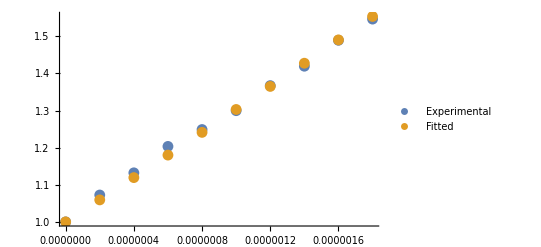

Linear Stern-Volver fit is:

1.01024+297502. x

```mathematica
Clear[concentrations,fluorescenceRatioPredicted];
fluorescenceRatioObserved=fluorescenceObserved[[1]]/fluorescenceObserved(*Observed fluorescence ratios*);
concentrations[K_]:=Flatten[Table[{Values[Solve[proteinConc0==proteinConc*(1+K*ligandConc)&&ligandConc0[[n]]==ligandConc*(1+proteinConc*K)&&proteinConc≥0&&ligandConc≥0&&K≥0,{proteinConc,ligandConc},Reals]]},{n,1,numberVials}],2];
epsilon=0(*Residual fluorescence of complex relatively to the free protein*);
fluorescenceRatioPredicted[K_]:=proteinConc0/(concentrations[K][[All,1]]+epsilon*K*concentrations[K][[All,1]]*concentrations[K][[All,2]])(*Calculated fluorescence ratio as function of K*);
Quiet[Ka=FindArgMin[{Norm[fluorescenceRatioPredicted[x]-fluorescenceRatioObserved]}, x, WorkingPrecision->20][[1]]](*Fitted binding constant*);
Print["Fitted binding constant Ka = ", Ka]
expCurve=Transpose[{ligandConc0,fluorescenceRatioObserved}];(*Experimental Stern-Volmer plot*)
Quiet[fittedCurve=Transpose[{ligandConc0,fluorescenceRatioPredicted[Ka]}]];(*Fitted Stern-Volmer plot*)
ListPlot[{expCurve,fittedCurve},PlotLegends->{"Experimental","Fitted"}]
Print["Linear Stern-Volver fit is:"]
Normal[LinearModelFit[expCurve,x,x]](*Returns fitted linear Stern-Volmer equation including apparent (incorrect) binding constant value*)
Quit[]
```

The fluorescence data example here is taken from l.Int. J. Pharm. Sci. Drug Res., July-August, 2022, Vol 14, Issue 4, 397-401. The slope of the Stern-Volmer plot exactly matches the constant reported in the paper, but when we take into account the fact that the equilibrium ligand concentration is different from the initial, the result becomes 12% higher.

## Titration of protein with ligand solution as we used in our studies

#### Input experimental details

```mathematica
fluorescenceObserved={100000,92362,87655,81648,78948,75518}(*Observed fluorescence intensities*);
volume0=2.3*^-3(*Initial volume of protein solution, L*);
proteinConc0=1.06*^-6(*Concentration of protein solution, M*);
ligandConc0=4.6*^-5(*Concentration of titrant (ligand solution), M*);
volumeInjected=0.01*^-3(*Volume of titrant added per step (injection), L*);
```

#### Run calculation

Fitted binding constant Ka = 424433.38369546730401

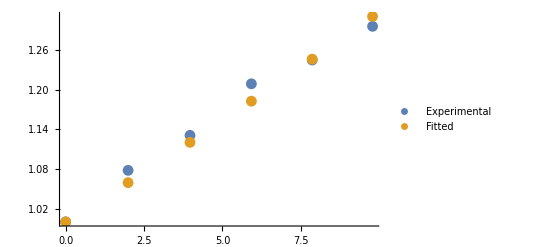

Linear Stern-Volver fit is:

1.01184+300709. x

```mathematica
Clear[concentrations,fluorescenceRatioPredicted];
numberInjections=Length[fluorescenceObserved]-1(*Number of steps*);
concentrationsTotal=Table[{proteinConc0*volume0/(volume0+volumeInjected*n),ligandConc0*volumeInjected*n/(volume0+volumeInjected*n)},{n,0,numberInjections}];
fluorescenceRatioObserved=(fluorescenceObserved[[1]]/concentrationsTotal[[1,1]])/(fluorescenceObserved/concentrationsTotal[[All,1]])(*Observed apparent fluorescence ratios*);
concentrations[K_]:=Flatten[Table[{Values[Solve[concentrationsTotal[[n,1]]==proteinConc*(1+K*ligandConc)&&concentrationsTotal[[n,2]]==ligandConc*(1+proteinConc*K)&&proteinConc≥0&&ligandConc≥0&&K≥0,{proteinConc,ligandConc},Reals]]},{n,1,numberInjections+1}],2];
epsilon=0(*Residual fluorescence of complex relatively to the free protein*);
fluorescenceRatioPredicted[K_]:=concentrationsTotal[[All,1]]/(concentrations[K][[All,1]]+epsilon*K*concentrations[K][[All,1]]*concentrations[K][[All,2]])(*Calculated apparent fluorescence ratio as function of K*);
Quiet[Ka=FindArgMin[{Norm[fluorescenceRatioPredicted[x]-fluorescenceRatioObserved]}, x, WorkingPrecision->20][[1]]](*Fitted binding constant*);
Print["Fitted binding constant Ka = ", Ka]
expCurve=Transpose[{concentrationsTotal[[All,2]],fluorescenceRatioObserved}];(*Experimental Stern-Volmer plot*)
Quiet[fittedCurve=Transpose[{concentrationsTotal[[All,2]],fluorescenceRatioPredicted[Ka]}]];(*Fitted Stern-Volmer plot*)
ListPlot[{expCurve,fittedCurve},PlotLegends->{"Experimental","Fitted"}]
Print["Linear Stern-Volver fit is:"]
Normal[LinearModelFit[expCurve,x,x]](*Returns fitted linear Stern-Volmer equation including apparent (incorrect) binding constant value*)
Quit[]
```

The true value here is more than 40% higher than the Stern-Volmer plot slope.